```mathematica
t = Import["data/c.dat","Table", Path -> NotebookDirectory[] ]
```

(26 | 0 | 0
27 | 3 | 2
29 | 8 | 2
31 | 2 | 4
34 | 2 | 2
35 | 0 | 2
37 | 0 | 5
38 | 0 | 2
40 | 0 | 1
42 | 0 | 3
44 | 0 | 3
46 | 0 | 0
51 | 4 | 0
52 | 1 | 0
54 | 2 | 0
55 | 2 | 0
57 | 4 | 2
58 | 0 | 2
59 | 1 | 0
61 | 0 | 4
63 | 1 | 2
65 | 2 | 2
67 | 3 | 0
70 | 1 | 0
71 | 2 | 0
73 | 9 | 0
75 | 8 | 0
76 | 4 | 0
77 | 2 | 0
80 | 0 | 6
83 | 10 | 0
86 | 0 | 1
87 | 3 | 3
88 | 4 | 5
91 | 0 | 9
92 | 4 | 0
94 | 0 | 1
95 | 0 | 0
97 | 0 | 3
98 | 0 | 3
100 | 0 | 1
101 | 0 | 0
102 | 1 | 0
106 | 3 | 0
107 | 2 | 0
108 | 7 | 1
110 | 0 | 2
112 | 1 | 1
113 | 3 | 1
114 | 1 | 2
116 | 4 | 2
118 | 1 | 0
119 | 4 | 0
121 | 5 | 1
123 | 4 | 4
124 | 2 | 1
127 | 1 | 1
128 | 2 | 0
130 | 2 | 2)

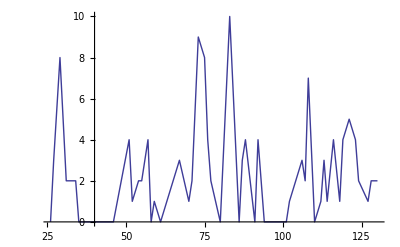

```mathematica
ListPlot[t[[All,{1,2}]],PlotJoined->True]
```

```mathematica
s=t[[All,{1,3}]]
```

(26 | 0
27 | 2
29 | 2
31 | 4
34 | 2
35 | 2
37 | 5
38 | 2
40 | 1
42 | 3
44 | 3
46 | 0
51 | 0
52 | 0
54 | 0
55 | 0
57 | 2
58 | 2
59 | 0
61 | 4
63 | 2
65 | 2
67 | 0
70 | 0
71 | 0
73 | 0
75 | 0
76 | 0
77 | 0
80 | 6
83 | 0
86 | 1
87 | 3
88 | 5
91 | 9
92 | 0
94 | 1
95 | 0
97 | 3
98 | 3
100 | 1
101 | 0
102 | 0
106 | 0
107 | 0
108 | 1
110 | 2
112 | 1
113 | 1
114 | 2
116 | 2
118 | 0
119 | 0
121 | 1
123 | 4
124 | 1
127 | 1
128 | 0
130 | 2)

```mathematica
y=Fit[s,{1,x,√x,x^2,x^3,x^-1,x^4,x^5},x]
```

-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x

```mathematica
y
```

-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x

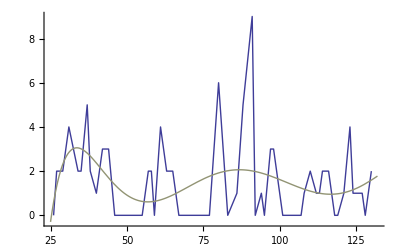

```mathematica
Show[{ListPlot[s,Joined->True],Plot[y,{x,25,132}, ColorFunction->"Rainbow"]}]
```

```mathematica
Clear[y]
```

```mathematica
y = Fit[s,{1,x,√x,x^2,x^3,x^-1,x^4,x^5},x]
```

-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x

```mathematica
Show[{ListPlot[s,Joined->True],Plot[y,{x,25,132}, ColorFunction->"Rainbow"]}]
```

-Graphics-

```mathematica
z = Fit[s,{1,Sin[x],Sin[2x],Sin[3x],Sin[4x]},x]
```

-0.613505 sin(x)-0.250358 sin(2 x)+0.141851 sin(3 x)-0.198662 sin(4 x)+1.53657

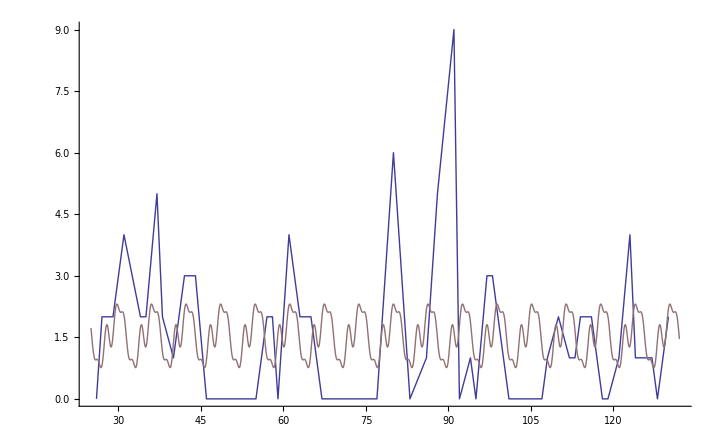

```mathematica
Show[{ListPlot[s,Joined->True],Plot[z,{x,25,132}, ColorFunction->"Rainbow"]}]
```

```mathematica
w = Fit[s,{1,x,√x,x^2,x^3,x^-1,x^4,x^5,Sin[x],Sin[2x],Sin[3x],Sin[4x]},x]
```

-2790.6-5.59186×10^-8 x^5+0.0000320158 x^4-0.00773903 x^3+1.08897 x^2-139.577 x+1089.1 √x+6587.35/x-0.518083 sin(x)-0.183214 sin(2 x)+0.228565 sin(3 x)-0.139054 sin(4 x)

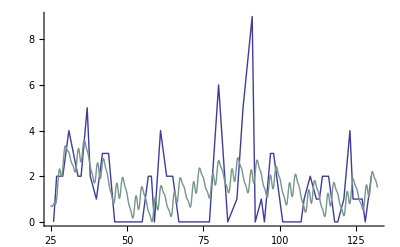

```mathematica
Show[{ListPlot[s,Joined->True],Plot[w,{x,25,132}, ColorFunction->"Rainbow"]}]
```

```mathematica
α = Fit[s,{1,Sin[y],Sin[2y],Sin[3y],Sin[4y]},x]
```

-1.10143 sin(2 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+0.640825 sin(3 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))-0.0289292 sin(4 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+0.0732009 sin(1816.99+4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x-2917.42/x)+1.81743

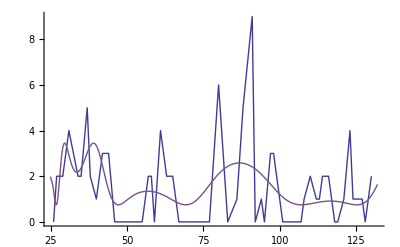

```mathematica
Show[{ListPlot[s,Joined->True],Plot[α,{x,25,132}, ColorFunction->"Rainbow"]}]
```

```mathematica
β = Fit[s,{1,x,√x,x^2,x^3,x^-1,x^4,x^5,Sin[y],Sin[2y],Sin[3y],Sin[4y]},x]
```

2.57993 sin(2 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+2.08031 sin(3 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+1.12517 sin(4 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))-6.69571 sin(1816.99+4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x-2917.42/x)-4571.18-1.62522×10^-7 x^5+0.0000929528 x^4-0.0218902 x^3+2.88515 x^2-320.967 x+2201.29 √x+2016.62/x

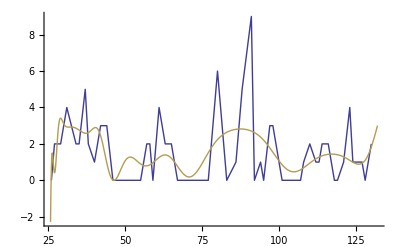

```mathematica
Show[{ListPlot[s,Joined->True],Plot[β,{x,25,132}, ColorFunction->"Rainbow"]}]
```

```mathematica
γ = Fit[s,{1,x,√x,x^2,x^3,x^-1,x^4,x^5,Sin[y],Sin[2y],Sin[3y],Sin[4y],Sin[x],Sin[2x],Sin[3x],Sin[4x]},x]
```

2.38143 sin(2 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+1.89432 sin(3 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+0.997943 sin(4 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))-6.15339 sin(1816.99+4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x-2917.42/x)-5279.71-1.58555×10^-7 x^5+0.0000912502 x^4-0.0217063 x^3+2.91199 x^2-335.865 x+2385.42 √x+5592.84/x-0.354649 sin(x)-0.229404 sin(2 x)+0.113864 sin(3 x)-0.00927061 sin(4 x)

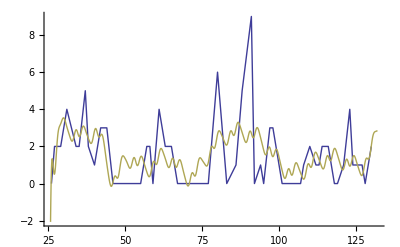

```mathematica
Show[{ListPlot[s,Joined->True],Plot[γ,{x,25,132}, ColorFunction->"Rainbow"]}]
```

```mathematica
δ = Fit[s,{y,z,w,α,β,γ},x]
```

-5.88719×10^-11 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x)+3.51826×10^-11 (-2790.6-5.59186×10^-8 x^5+0.0000320158 x^4-0.00773903 x^3+1.08897 x^2-139.577 x+1089.1 √x+6587.35/x-0.518083 sin(x)-0.183214 sin(2 x)+0.228565 sin(3 x)-0.139054 sin(4 x))+1.23133×10^-10 (2.57993 sin(2 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+2.08031 sin(3 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+1.12517 sin(4 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))-6.69571 sin(1816.99+4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x-2917.42/x)-4571.18-1.62522×10^-7 x^5+0.0000929528 x^4-0.0218902 x^3+2.88515 x^2-320.967 x+2201.29 √x+2016.62/x)+1. (2.38143 sin(2 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+1.89432 sin(3 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+0.997943 sin(4 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))-6.15339 sin(1816.99+4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x-2917.42/x)-5279.71-1.58555×10^-7 x^5+0.0000912502 x^4-0.0217063 x^3+2.91199 x^2-335.865 x+2385.42 √x+5592.84/x-0.354649 sin(x)-0.229404 sin(2 x)+0.113864 sin(3 x)-0.00927061 sin(4 x))+1.89613×10^-11 (-1.10143 sin(2 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+0.640825 sin(3 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))-0.0289292 sin(4 (-1816.99-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x+2917.42/x))+0.0732009 sin(1816.99+4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x-2917.42/x)+1.81743)+3.27788×10^-11 (-0.613505 sin(x)-0.250358 sin(2 x)+0.141851 sin(3 x)-0.198662 sin(4 x)+1.53657)

```mathematica
Show[{ListPlot[s,Joined->True],Plot[δ,{x,25,132}, ColorFunction->"Rainbow"]}]
```

-Graphics-

```mathematica
η = Fit[s,{δ,π^δ},x]
```

0.86508 (-5.88719×10^-11 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x)+3.27788×10^-11 (-0.613505 sin(x)-0.250358 sin(2 x)+0.141851 sin(3 x)-0.198662 sin(4 x)+1.53657)+3.51826×10^-11 (-5.59186×10^-8 x^5+0.0000320158 x^4-0.00773903 x^3+1.08897 x^2-139.577 x+1089.1 √x-0.518083 sin(x)-0.183214 sin(2 x)+0.228565 sin(3 x)-0.139054 sin(4 x)-2790.6+6587.35/x)+1.23133×10^-10 (-1.62522×10^-7 x^5+0.0000929528 x^4-0.0218902 x^3+2.88515 x^2-320.967 x+2201.29 √x+2.57993 sin(2 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+2.08031 sin(3 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+1.12517 sin(4 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))-6.69571 sin(4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x+1816.99-2917.42/x)-4571.18+2016.62/x)+1. (-1.58555×10^-7 x^5+0.0000912502 x^4-0.0217063 x^3+2.91199 x^2-335.865 x+2385.42 √x-0.354649 sin(x)-0.229404 sin(2 x)+0.113864 sin(3 x)-0.00927061 sin(4 x)+2.38143 sin(2 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+1.89432 sin(3 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+0.997943 sin(4 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))-6.15339 sin(4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x+1816.99-2917.42/x)-5279.71+5592.84/x)+1.89613×10^-11 (-1.10143 sin(2 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+0.640825 sin(3 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))-0.0289292 sin(4 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+0.0732009 sin(4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x+1816.99-2917.42/x)+1.81743))+0.0181138 π^(-5.88719×10^-11 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x)+3.27788×10^-11 (-0.613505 sin(x)-0.250358 sin(2 x)+0.141851 sin(3 x)-0.198662 sin(4 x)+1.53657)+3.51826×10^-11 (-5.59186×10^-8 x^5+0.0000320158 x^4-0.00773903 x^3+1.08897 x^2-139.577 x+1089.1 √x-0.518083 sin(x)-0.183214 sin(2 x)+0.228565 sin(3 x)-0.139054 sin(4 x)-2790.6+6587.35/x)+1.23133×10^-10 (-1.62522×10^-7 x^5+0.0000929528 x^4-0.0218902 x^3+2.88515 x^2-320.967 x+2201.29 √x+2.57993 sin(2 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+2.08031 sin(3 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+1.12517 sin(4 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))-6.69571 sin(4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x+1816.99-2917.42/x)-4571.18+2016.62/x)+1. (-1.58555×10^-7 x^5+0.0000912502 x^4-0.0217063 x^3+2.91199 x^2-335.865 x+2385.42 √x-0.354649 sin(x)-0.229404 sin(2 x)+0.113864 sin(3 x)-0.00927061 sin(4 x)+2.38143 sin(2 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+1.89432 sin(3 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+0.997943 sin(4 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))-6.15339 sin(4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x+1816.99-2917.42/x)-5279.71+5592.84/x)+1.89613×10^-11 (-1.10143 sin(2 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+0.640825 sin(3 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))-0.0289292 sin(4 (-4.82016×10^-8 x^5+0.0000274264 x^4-0.00651157 x^3+0.883237 x^2-105.419 x+774.988 √x-1816.99+2917.42/x))+0.0732009 sin(4.82016×10^-8 x^5-0.0000274264 x^4+0.00651157 x^3-0.883237 x^2+105.419 x-774.988 √x+1816.99-2917.42/x)+1.81743))

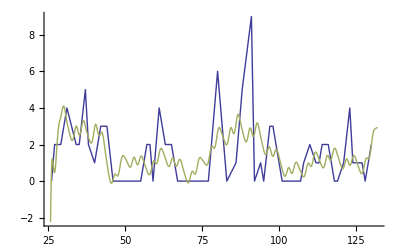

```mathematica
Show[{ListPlot[s,Joined->True],Plot[η,{x,25,132}, ColorFunction->"Rainbow"]}]
```

```mathematica
t=Import["data/12term41.dat","Table", Path -> NotebookDirectory[]]
```

(31 | 1 | 2
32 | 1 | 3
34 | 4 | 5
36 | 2 | 9
38 | 3 | 0
39 | 2 | 2
41 | 1 | 0
43 | 0 | 5
45 | 0 | 3
46 | 0 | 1
48 | 0 | 2
52 | 4 | 0
53 | 2 | 0
55 | 0 | 0
55 | 3 | 0
57 | 5 | 0
58 | 2 | 1
60 | 1 | 3
61 | 1 | 5
64 | 1 | 1
65 | 2 | 1
67 | 7 | 0
68 | 2 | 1
70 | 2 | 0
70 | 5 | 2
72 | 2 | 2
74 | 7 | 0
75 | 5 | 0
76 | 7 | 0
79 | 1 | 8
82 | 12 | 4)

```mathematica
Dimensions[t]
```

{31,3}

```mathematica
MatrixForm[s=Table[If[j==1,t[[i,1]],18+Sum[t[[n,2]]-t[[n,3]],{n,1,i}]],{i,31},{j,2}]]
```

(31 | 17
32 | 15
34 | 14
36 | 7
38 | 10
39 | 10
41 | 11
43 | 6
45 | 3
46 | 2
48 | 0
52 | 4
53 | 6
55 | 6
55 | 9
57 | 14
58 | 15
60 | 13
61 | 9
64 | 9
65 | 10
67 | 17
68 | 18
70 | 20
70 | 23
72 | 23
74 | 30
75 | 35
76 | 42
79 | 35
82 | 43)

```mathematica
k=3
f = NonlinearFit[s,∑_(n=1)^k Subscript[q, n+k] x^Subscript[q, n],{x},Table[Subscript[q, i],{i,1,2k}]]
```

3

FindFit::cvmit: Failed to converge to the requested accuracy or precision within TraditionalForm`100 iterations.

0.00705767 x^2.73123-0.0357458 x^2.39977+0.429875 x^1.45147

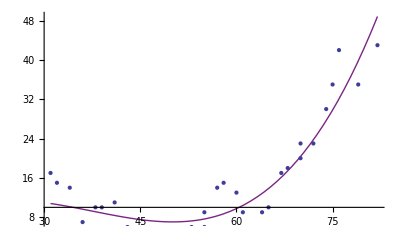

```mathematica
Show[Plot[f,{x,31,82}, ColorFunction->"Rainbow"],ListPlot[s]]
```

```mathematica
k=2
g = NonlinearFit[s,∑_(n=1)^k Subscript[q, n+2k]*Sin[Subscript[q, n+k] x^Subscript[q, n]],{x},Table[Subscript[q, i],{i,1,3k}]]
```

2

FindFit::cvmit: Failed to converge to the requested accuracy or precision within TraditionalForm`100 iterations.

-2.40001 sin(0.716906 x^1.12775)-2.39993 sin(0.716885 x^1.12775)

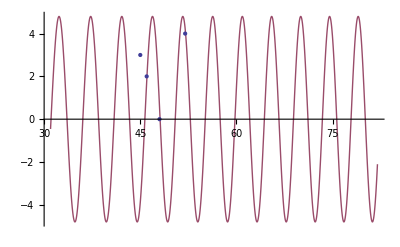

```mathematica
Show[Plot[g,{x,31,82}, ColorFunction->"Rainbow"],ListPlot[s]]
```